## Setup

### Model setup

Cubic reaction kinetics in (n,η) variables

```mathematica
f=η-n^3+n;
source=p-n; (*source in v*)
```

```mathematica
fixedParams={p->0,Dv->10,Du->1,T->10^10};
params=Join[{eps->10^-6,L->20000},fixedParams];
```

## Comsol import

### Import

```mathematica
Import[NotebookDirectory[]<>"cubicModel-linSourceV-L-20000-dx-0_5-p-0-seed-1-pbc.h5","StructureGraph"]
```

-Graphics-

```mathematica
rhoComsol=Import[NotebookDirectory[]<>"cubicModel-linSourceV-L-20000-dx-0_5-p-0-seed-1-pbc.h5",{"Data","data"}];
tComsol=Import[NotebookDirectory[]<>"cubicModel-linSourceV-L-20000-dx-0_5-p-0-seed-1-pbc.h5",{"Data","times"}];
xComsol=Import[NotebookDirectory[]<>"cubicModel-linSourceV-L-20000-dx-0_5-p-0-seed-1-pbc.h5",{"Data","grid"}];
```

### Wavelength distribution (first run only)

```mathematica
peaksComsol=Table[Block[{peaks},
peaks=FindPeaks[rhoComsol[[ind]]];
If[peaks[[1,1]]==1,
peaks[[2;;,1]],
If[peaks[[-1,1]]==Length@xComsol,
peaks[[;;-2,1]],
peaks[[All,1]]
]
]
],
{ind,1,Length@rhoComsol}];
```

```mathematica
troughsComsol=Table[
Block[{troughs},
troughs=FindPeaks[-rhoComsol[[ind]]];
If[troughs[[1,1]]==1,
troughs[[2;;,1]],
If[troughs[[-1,1]]==Length@xComsol,
troughs[[;;-2,1]],
troughs[[All,1]]
]
]
],
{ind,1,Length@rhoComsol}];
```

first timestep at which all mesas and troughs are found such that the (half-) wavelengths can be calculated.

```mathematica
indStart=1+First@Last@Position[(Length@#[[1]]==Length@#[[2]])&/@Transpose[{troughsComsol,peaksComsol}],_?(#==False&)]
```

5

```mathematica
plotStart=15;
```

Mean wavelength

```mathematica
wavelengthUpDownComsol=Transpose@{Log10@tComsol[[Max[plotStart,indStart];;]],
((Mean@Abs@First@Differences@#)&/@Transpose[{troughsComsol,peaksComsol}][[Max[plotStart,indStart];;]])*0.5*2};
```

All wavelengths

```mathematica
ClearAll@wavelengthsUpDownComsol;
wavelengthsUpDownComsol=Transpose@{Log10@tComsol[[Max[plotStart,indStart];;]],
((Abs@First@Differences@#)&/@Transpose[{troughsComsol,peaksComsol}][[Max[plotStart,indStart];;]])*0.5*2};
If[indStart>plotStart,
wavelengthsUpDownComsol=Join[Transpose@{Log10@tComsol[[Range[15,indStart-1]]],Array[{}&,indStart-15]},wavelengthsUpDownComsol];]
```

Histogram over wavelength over time

```mathematica
wavelengthLogHist=Flatten/@Flatten[(Transpose@{Array[1&,Length@#[[2]]]*#[[1]],#[[2]]})&/@Transpose@{Log10@tComsol[[15;;]],(Transpose[{MovingAverage[#[[1]],2],Log10[1+#]&/@#[[2]]}&@HistogramList[If[#==={},{-1},#],{-0.5,70,1}]])&/@wavelengthsUpDownComsol[[All,2]]},1];
```

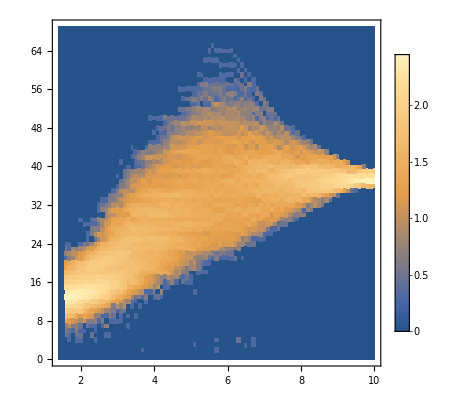

```mathematica
Show[ListDensityPlot[wavelengthLogHist, PlotLegends->Automatic,InterpolationOrder->0],
ListPlot[{Log10@#[[1]],#[[2]]}&/@wavelengthLogHist,Joined->True,PlotStyle->Black]
]
```

### Average over seven runs (first + 6 more)

We plot the evolution starting at the 14th timestep, t=10^1.4 approx 25.
contributedTimes counts how many of the runs contributed to the histogram at a timestep t (We only let a run contribute at t if the same number of mesas and troughs is found due to periodic boundary conditions.)

```mathematica
contributedTimes=If[indStart>plotStart,Join[Array[0&,indStart-15],Array[1&,(Length@tComsol)-indStart+1]],
Array[1&,(Length@tComsol)-plotStart+1]];
wavelengthsTot=wavelengthsUpDownComsol;
Block[{run},For[run=2,run≤ 7,run++,
Block[{rhoRun,peaksRun,zerosRun,troughsRun,wavelengths,correctCountInd,
indTest},
rhoRun=Import[NotebookDirectory[]<>"cubicModel-linSourceV-L-20000-dx-0_5-p-0-seed-"<>ToString[run]<>"-pbc.h5",{"Data","data"}];

peaksRun=Array[{}&,Length[tComsol]-14];
troughsRun=Array[{}&,Length[tComsol]-14];
Do[Block[{peaks,troughs,zeros},
peaks=FindPeaks[rhoRun[[ind]]];
troughs=FindPeaks[-rhoRun[[ind]]];
(*account for periodic boundary conditions: (The Padding->"Periodic" option to FindPeaks does not work for Interp. Order=1 and higher Interp. Order finds often two instead of one maximum probably because the mesas are so flat)*)
(*two peaks (means two high-density mesas) found on the outsides*)
If[peaks[[1,1]]<troughs[[1,1]]&&peaks[[-1,1]]>troughs[[-1,1]],

troughsRun[[ind-14]]=troughs[[All,1]];
If[peaks[[1,2]]>peaks[[-1,2]],
peaksRun[[ind-14]]=peaks[[;;-2,1]];,
peaksRun[[ind-14]]=peaks[[2;;,1]];],

(*two troughs found on the outsides*)
If[peaks[[1,1]]>troughs[[1,1]]&&peaks[[-1,1]]<troughs[[-1,1]],

peaksRun[[ind-14]]=peaks[[All,1]];
If[troughs[[1,2]]<troughs[[-1,2]],
troughsRun[[ind-14]]=troughs[[;;-2,1]];,
troughsRun[[ind-14]]=troughs[[2;;,1]];],

(*if the periodicity fits*)
peaksRun[[ind-14]]=peaks[[All,1]];
troughsRun[[ind-14]]=troughs[[All,1]];
]
];
],{ind,15,Length@tComsol}];

Print["Run: ", run,", time indices of wrongly-determined peaks: ",Flatten@Position[(Length@#[[1]]==Length@#[[2]])&/@Transpose[{troughsRun,peaksRun}],_?(#==False&)] ,", number of nonmatching findings: ", Length@Flatten@Position[(Length@#[[1]]==Length@#[[2]])&/@Transpose[{troughsRun,peaksRun}],_?(#==False&)]];

(*treat cases where peak detection did not work*)
correctCountInd=Flatten@Position[(Length@#[[1]]==Length@#[[2]])&/@Transpose[{troughsRun,peaksRun}],_?(#==True&)];

wavelengths=
((Abs@First@Differences@#)&/@Transpose[{troughsRun,peaksRun}][[correctCountInd]])*0.5*2;
Do[
wavelengthsTot[[correctCountInd[[tt]],2]]=Join[wavelengthsTot[[correctCountInd[[tt]],2]],wavelengths[[tt]]];
contributedTimes[[correctCountInd[[tt]]]]+=1,
{tt,Length@correctCountInd}];
];
]];
```

Run: 2, time indices of wrongly-determined peaks: {}, number of nonmatching findings: 0

Run: 3, time indices of wrongly-determined peaks: {49,50,51}, number of nonmatching findings: 3

Run: 4, time indices of wrongly-determined peaks: {}, number of nonmatching findings: 0

Run: 5, time indices of wrongly-determined peaks: {}, number of nonmatching findings: 0

Run: 6, time indices of wrongly-determined peaks: {19}, number of nonmatching findings: 1

Run: 7, time indices of wrongly-determined peaks: {}, number of nonmatching findings: 0

```mathematica
contributedTimes
```

{6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7}

Mean wavelength

```mathematica
meanWavelengthTot={#[[1]],Mean@#[[2]]}&/@wavelengthsTot;
```

Log histogram

```mathematica
wavelengthLogHistTot=Flatten[Table[
Block[{hist,logHist,txHist},
hist = HistogramList[wavelengthsTot[[tt,2]],{-0.5,70,1}];
logHist={MovingAverage[#[[1]],2],Log10[1+#[[2]]/contributedTimes[[tt]]]}&@hist;
Transpose[Join[
{Array[Log10[tComsol[[tt+14]]]&,Length@logHist[[1]]]},
logHist
]]
],
{tt,Length@contributedTimes}],1];
```

## Lambda_stop threshold

#### Analytic expression for growth rate in diff- and react-limited regimes

```mathematica
σD=8 Dv/(√(Du/2) L(1-ξ))Exp[-2ξ L/√(Du/2)]/.ξ->(p+1)/2;
```

```mathematica
lambdaStop=Table[{σD 2/(1-p)/.L->ll,2ll}/.params,{ll,Range[5,30,1]}];
```

## fastest-growing mode

```mathematica
qFastest=q/.Last@Maximize[Eigenvalues[{{-eps,-Dv q^2},{Du q^2-1-eps,-(Dv+Du)q^2-1}}][[2]],q,PositiveReals];
```

```mathematica
lInit=2.Pi/qFastest/.fixedParams;
```

## Plot

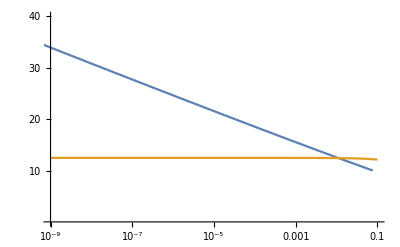

```mathematica
ListLogLinearPlot[{lambdaStop,{10^#,lInit/.eps->10^#}&/@Range[-9,-1,0.01]}/.params,Joined->True,
PlotRange->{{10^-9,10^-1},{0,40}},
Ticks->{{10^-9,10^-7,10^-5,10^-3,10^-1},{10,20,30,40}}]
```

```mathematica
myRed=RGBColor["#ca3300"]
myCol=Blend[Reverse@{myRed,White},#]&;
```

RGBColor[0.792156862745098, 0.2, 0.]

```mathematica
Show[ListDensityPlot[wavelengthLogHistTot,PlotLegends->Automatic,InterpolationOrder->0,
ColorFunction->myCol],
ListPlot[{meanWavelengthTot,{{1.4,lInit/.params},{10,lInit/.params}},
{{1.4,lambda},{10,lambda}}/.(FindRoot[eps==σD 2/(1-p)/.L->(lambda/2)/.params,{lambda,20}])},
Joined->True,PlotStyle->{Black,Red,Blue}]
]
```

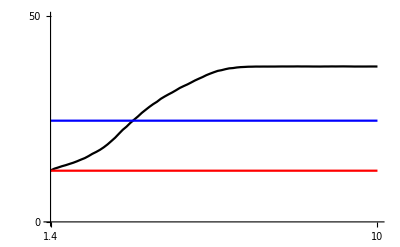

```mathematica
ListPlot[{meanWavelengthTot,{{1.4,lInit/.params},{10,lInit/.params}},
{{1.4,lambda},{10,lambda}}/.(FindRoot[eps==σD 2/(1-p)/.L->(lambda/2)/.params,{lambda,20}])},Joined->True,PlotStyle->{Black,Red,Blue},
Ticks->{{1.4,10},{0,50}},
PlotRange->{{1.4,10},{0,50}}]
```

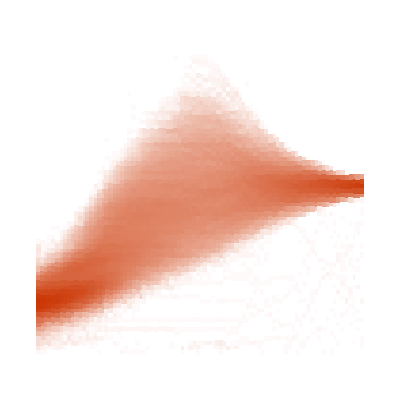

```mathematica
ListDensityPlot[wavelengthLogHistTot,InterpolationOrder->0,
ColorFunction->myCol,Frame->None,
PlotRange->{{1.45,10.05},{-0.5,70.5}}]
```

```mathematica
ListDensityPlot[rhoComsol[[All,;;3000]],
ColorFunction->GrayLevel,Frame->None,PlotLegends->Automatic]
```

-Graphics-

x goes in space from 0 to 1500

t goes from 1 to 10^10